## Example of a sequence β^{(9)} with a unique 9 - atomic measure supported on the curve y^2=x(x^2+3).

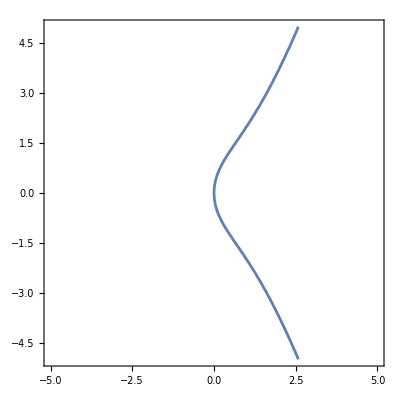

```mathematica
Clear["Global`*"]
ContourPlot[y^2==x(x^2+3),{x,-5,5},{y,-5,5}]
```

```mathematica
FindInstance[y^2==x(x^2+3)&& 0<y<11/10,{x,y},Reals]
```

{{x→3/16,y→(3 √259)/64}}

### The atoms of the measure are the following :

```mathematica
xp[1]=oo;yp[1]=oo;
xp[2]=1;yp[2]=2;
xp[3]=1;yp[3]=-2;
xp[4]=3;yp[4]=6;
xp[5]=3;yp[5]=-6;
xp[6]=12;yp[6]=42;
xp[7]=12;yp[7]=-42;
xp[8]=3/16;yp[8]=(3 √259)/64;
xp[9]=3/16;yp[9]=-(3 √259)/64;

Table[yp[i]^2 -xp[i](xp[i]^2+3),{i,1,9}]//.{oo->0}
```

{0,0,0,0,0,0,0,0,0}

### The moments in the sequence are :

```mathematica
s[i_,j_]:=Sum[(xp[k]^i  yp [k]^j  ),{k,1,9}]

s00=s[0,0]; s10=s[1,0]; s01=s[0,1]; s20=s[2,0]; s11=s[1,1];s02=s[0,2];
s30=s[3,0];s21=s[2,1];s12=s[1,2];s03=s[0,3];
s40=s[4,0];s31=s[3,1];s22=s[2,2];s13=s[1,3];s04=s[0,4];
s50=s[5,0];s41=s[4,1];s32=s[3,2];s23=s[2,3];s14=s[1,4];s05=s[0,5];
s60=s[6,0];s51=s[5,1];s42=s[4,2];s33=s[3,3];s24=s[2,4];s15=s[1,5];s06=s[0,6];


M4:=({{s00, s10, s01, s20, s11, s02, s30, s21, s12, s03, s40, s31, s22, s13, s04}, {s10, s20, s11, s30, s21, s12, s40, s31, s22, s13, s50, s41, s32, s23, s14}, {s01, s11, s02, s21, s12, s03, s31, s22, s13, s04, s41, s32, s23, s14, s05}, {s20, s30, s21, s40, s31, s22, s50, s41, s32, s23, s60, s51, s42, s33, s24}, {s11, s21, s12, s31, s22, s13, s41, s32, s23, s14, s51, s42, s33, s24, s15}, {s02, s12, s03, s22, s13, s04, s32, s23, s14, s05, s42, s33, s24, s15, s06}, {s30, s40, s31, s50, s41, s32, s60, s51, s42, s33, s70, s61, s52, s43, s34}, {s21, s31, s22, s41, s32, s23, s51, s42, s33, s24, s61, s52, s43, s34, s25}, {s12, s22, s13, s32, s23, s14, s42, s33, s24, s15, s52, s43, s34, s25, s16}, {s03, s13, s04, s23, s14, s05, s33, s24, s15, s06, s43, s34, s25, s16, s07}, {s40, s50, s41, s60, s51, s42, s70, s61, s52, s43, s80, s71, s62, s53, s44}, {s31, s41, s32, s51, s42, s33, s61, s52, s43, s34, s71, s62, s53, s44, s35}, {s22, s32, s23, s42, s33, s24, s52, s43, s34, s25, s62, s53, s44, s35, s26}, {s13, s23, s14, s33, s24, s15, s43, s34, s25, s16, s53, s44, s35, s26, s17}, {s04, s14, s05, s24, s15, s06, s34, s25, s16, s07, s44, s35, s26, s17, s08}})//.{oo->0}
M3=M4[[Range[1,10],Range[1,10]]];
M2=M4[[Range[1,6],Range[1,6]]];
M1=M4[[Range[1,3],Range[1,3]]];
```

### The matrix M (3) is the following .

```mathematica
M3//MatrixForm
```

(9 | 259/8 | 0 | 39433/128 | 0 | 7391515/2048 | 7192603/2048 | 0 | 1394613073/32768 | 0
259/8 | 39433/128 | 0 | 7192603/2048 | 0 | 1394613073/32768 | 1364328529/32768 | 0 | 266699035123/524288 | 0
0 | 0 | 7391515/2048 | 0 | 1394613073/32768 | 0 | 0 | 266699035123/524288 | 0 | 52227613059289/8388608
39433/128 | 7192603/2048 | 0 | 1364328529/32768 | 0 | 266699035123/524288 | 261175116019/524288 | 0 | 51156550219225/8388608 | 0
0 | 0 | 1394613073/32768 | 0 | 266699035123/524288 | 0 | 0 | 51156550219225/8388608 | 0 | 10024522404641419/134217728
7391515/2048 | 1394613073/32768 | 0 | 266699035123/524288 | 0 | 52227613059289/8388608 | 51156550219225/8388608 | 0 | 10024522404641419/134217728 | 0
7192603/2048 | 1364328529/32768 | 0 | 261175116019/524288 | 0 | 51156550219225/8388608 | 50108745908953/8388608 | 0 | 9819697545666955/134217728 | 0
0 | 0 | 266699035123/524288 | 0 | 51156550219225/8388608 | 0 | 0 | 9819697545666955/134217728 | 0 | 1924557253200457633/2147483648
1394613073/32768 | 266699035123/524288 | 0 | 51156550219225/8388608 | 0 | 10024522404641419/134217728 | 9819697545666955/134217728 | 0 | 1924557253200457633/2147483648 | 0
0 | 0 | 52227613059289/8388608 | 0 | 10024522404641419/134217728 | 0 | 0 | 1924557253200457633/2147483648 | 0 | 377206599821592244195/34359738368)

### It is really positive semidefinite .

```mathematica
Det[M3[[{1,2,3,4,5,6,7},{1,2,3,4,5,6,7}]]]//Together
Det[M3[[{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,6,8,9,10}]]]//Together
N[Eigenvalues[M3]]
```

0

96819394028234448119970168802110931875/70368744177664

{1.10518×10^10,9.08431×10^8,3252.49,2273.75,9.47854,8.63922,1.44092,0.193918,0.00890874,0.}

### It is really (y^2 - x (x^2 + 3)) - pure .

```mathematica
M3//RowReduce//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### We check that the matrix N, called BVk in the code, is indeed positive semidefinite and singular .

```mathematica
colm3[i_]:=M4[[{1,2,3,4,5,6,7,8,9,10},{i}]]
pp=y^2 -x(x^2 +3);
s70=s[7,0];
s61=s[6,1];
s52=s[5,2];
s43=s[4,3];
s61=s[6,1];
s52=s[5,2];
s43=s[4,3];
s34=s[3,4];
Lqx=s20+3s00;
s[2,0]+3*s[0,0]-Lqx;
R1=M4[[{1},{2,3,4,5,7,8,9,12,13}]];
R2={{s01,Lqx,s11,s02,s21,s12,s03,s22,s13}};
R3=M4[[{2,3,4,5,6,8,9},{2,3,4,5,7,8,9,12,13}]];
R1;
Bk=M4[[{1,2,3,4,5,6,8,9,10},{1,2,3,4,5,6,8,9,10}]]//.{oo->0};
BVk=Join[Join[R1,R2,1],R3,1]//.{oo->0};
BVk//MatrixForm
Eigenvalues[BVk]//N
```

(259/8 | 0 | 39433/128 | 0 | 7192603/2048 | 0 | 1394613073/32768 | 0 | 266699035123/524288
0 | 42889/128 | 0 | 7391515/2048 | 0 | 1394613073/32768 | 0 | 266699035123/524288 | 0
39433/128 | 0 | 7192603/2048 | 0 | 1364328529/32768 | 0 | 266699035123/524288 | 0 | 51156550219225/8388608
0 | 7391515/2048 | 0 | 1394613073/32768 | 0 | 266699035123/524288 | 0 | 51156550219225/8388608 | 0
7192603/2048 | 0 | 1364328529/32768 | 0 | 261175116019/524288 | 0 | 51156550219225/8388608 | 0 | 9819697545666955/134217728
0 | 1394613073/32768 | 0 | 266699035123/524288 | 0 | 51156550219225/8388608 | 0 | 9819697545666955/134217728 | 0
1394613073/32768 | 0 | 266699035123/524288 | 0 | 51156550219225/8388608 | 0 | 10024522404641419/134217728 | 0 | 1924557253200457633/2147483648
0 | 266699035123/524288 | 0 | 51156550219225/8388608 | 0 | 9819697545666955/134217728 | 0 | 1885269022632092833/2147483648 | 0
266699035123/524288 | 0 | 51156550219225/8388608 | 0 | 9819697545666955/134217728 | 0 | 1924557253200457633/2147483648 | 0 | 369507766614827634403/34359738368)

{1.08293×10^10,8.84037×10^8,4840.35,1313.53,15.7512,2.5425,1.03432,0.0675627,0.}